```mathematica
(* Narrowband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-2 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootNB;
err=0.01;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

NB3; p=1

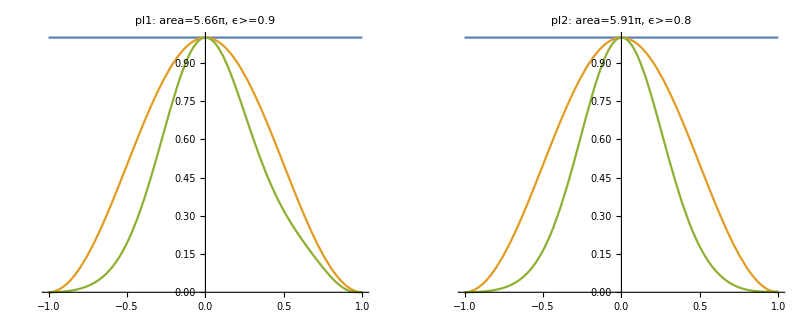

NB3; p=1/2

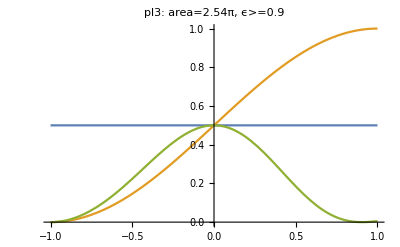

NB3; p=1/4

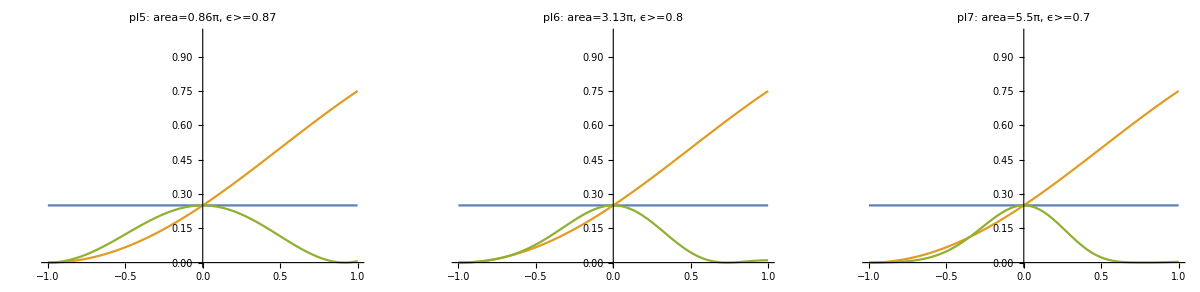

```mathematica
(*N=3*)
sequence=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];

pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,3]]

pl1=pltN[1.0,{Δ1->2.1981,Δ2->-10.7012,Ω1->1.8859},"pl1"];
pl2=pltN[1.0,{Δ1->2.2070,Δ2->-16.8304,Ω1->1.9690},"pl2"];

pl3=pltN[0.5,{Δ1->0.3403,Δ2->12.9362,Ω1->0.8472},"pl3"];

pl4=pltN[0.25,{Δ1->0.2304,Δ2->0.4925,Ω1->0.2867},"pl5"];
pl5=pltN[0.25,{Δ1->0.2394,Δ2->22.8659,Ω1->1.0439},"pl6"];
pl6=pltN[0.25,{Δ1->8.3479,Δ2->2.0459,Ω1->1.8320},"pl7"];

GGrid[Text[Style["NB3; p=1",FontSize->20]],{{pl1,pl2,Null, Null, Null}},ImageSize->Full]
GGrid[Text[Style["NB3; p=1/2",FontSize->20]],{{pl3, Null,  Null, Null, Null}},ImageSize->Full]
GGrid[Text[Style["NB3; p=1/4",FontSize->20]],{{pl4,pl5,pl6, Null, Null}},ImageSize->Full]
```

NB4; p=1

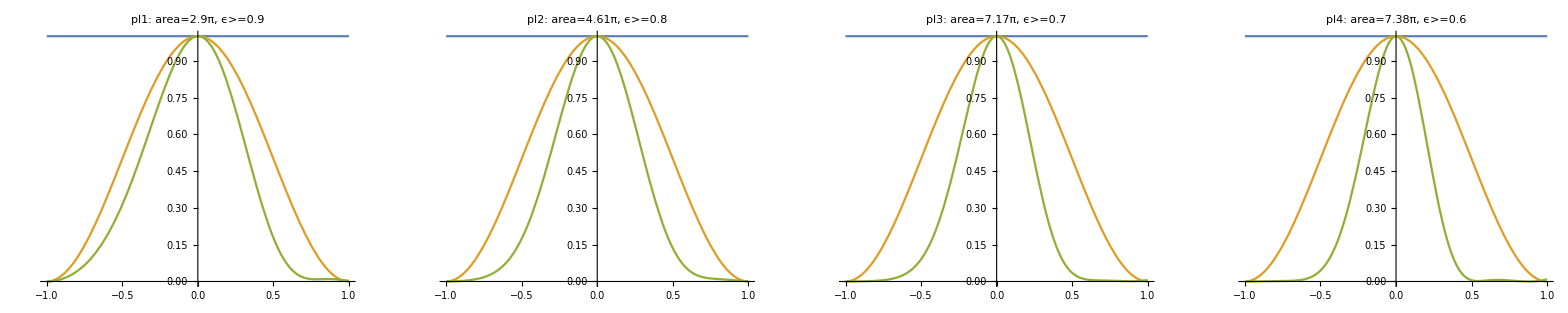

NB4; p=1/2

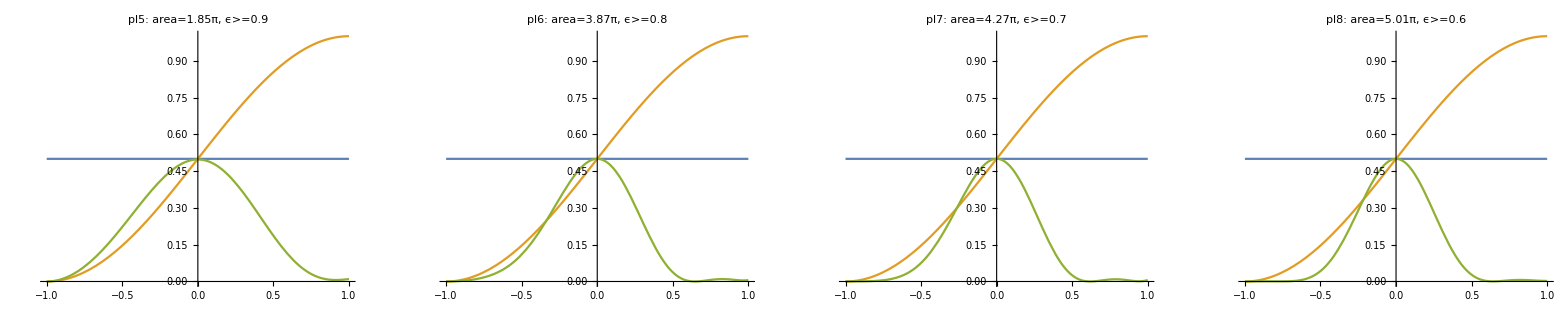

NB4; p=1/4

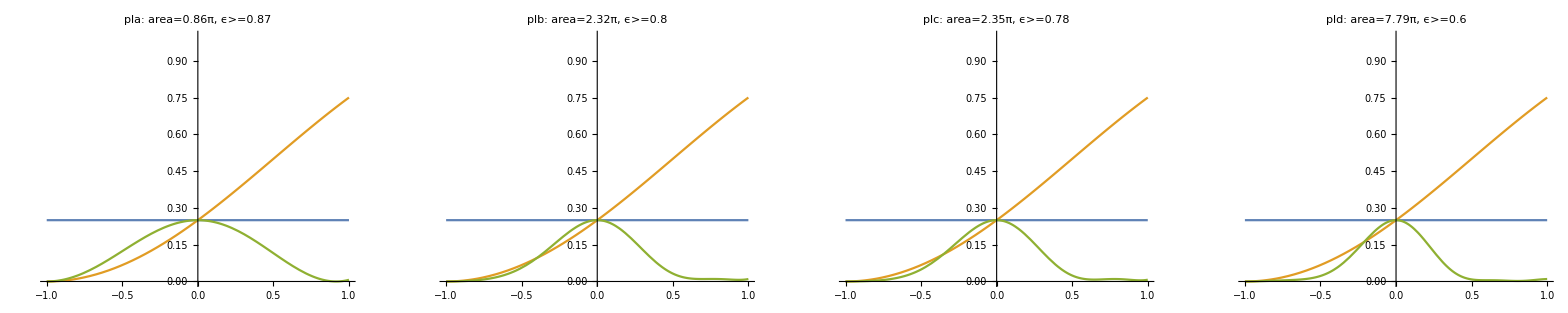

```mathematica
(*N=4*)
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,4]]

pl1=pltN[1.0,{Δ1->0.3889,Δ2->-2.2932,Δ3->1.0812,Δ4->0.7777,Ω1->0.7252},"pl1"];
pl2=pltN[1.0,{Δ1->-0.8023,Δ2->-3.2962,Δ3->17.0571,Δ4->-0.7616,Ω1->1.1515},"pl2"];
pl3=pltN[1.0,{Δ1->8.4042,Δ2->-2.0140,Δ3->8.3954,Δ4->-1.9170,Ω1->1.7933},"pl3"];
pl4=pltN[1.0,{Δ1->1.8370,Δ2->-8.3289,Δ3->1.8991,Δ4->-8.3425,Ω1->1.8442},"pl4"];

pl5=pltN[0.5,{Δ1->-0.6058,Δ2->0.520,Δ3->1.3883,Δ4->-0.4402,Ω1->0.4633},"pl5"];
pl6=pltN[0.5,{Δ1->0.6040,Δ2->4.8138,Δ3->-0.0827,Δ4->4.3399,Ω1->0.9686},"pl6"];
pl7=pltN[0.5,{Δ1->0.3681,Δ2->22.9591,Δ3->5.7137,Δ4->0.3651,Ω1->1.0684},"pl7"];
pl8=pltN[0.5,{Δ1->-0.3465,Δ2->31.0750,Δ3->-7.6846,Δ4->-0.3520,Ω1->1.2516},"pl8"];

pla=pltN[0.25,{Δ1->0.1262,Δ2->0.3311,Δ3->0.3314,Δ4->0.1258,Ω1->0.2149},"pla"];
plb=pltN[0.25,{Δ1->-0.5637,Δ2->1.0502,Δ3->0.7020,Δ4->-0.6103,Ω1->0.5799},"plb"];
plc=pltN[0.25,{Δ1->-0.5921,Δ2->0.7272,Δ3->1.0075,Δ4->-0.5560,Ω1->0.5864},"plc"];
pld=pltN[0.25,{Δ1->-8.7819,Δ2->14.7201,Δ3->1.6564,Δ4->6.0788,Ω1->-1.9472},"pld"];

GGrid[Text[Style["NB4; p=1",FontSize->20]],{{pl1,pl2,pl3,pl4}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/2",FontSize->20]],{{pl5,pl6,pl7,pl8}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/4",FontSize->20]],{{pla,plb,plc,pld}},ImageSize->Full]
```

NB5; p=1

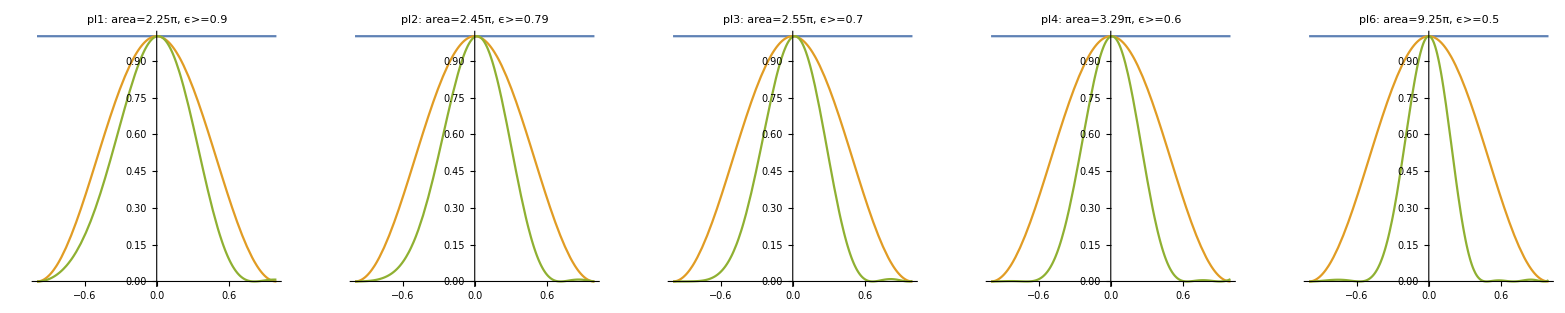

NB5; p=1/2

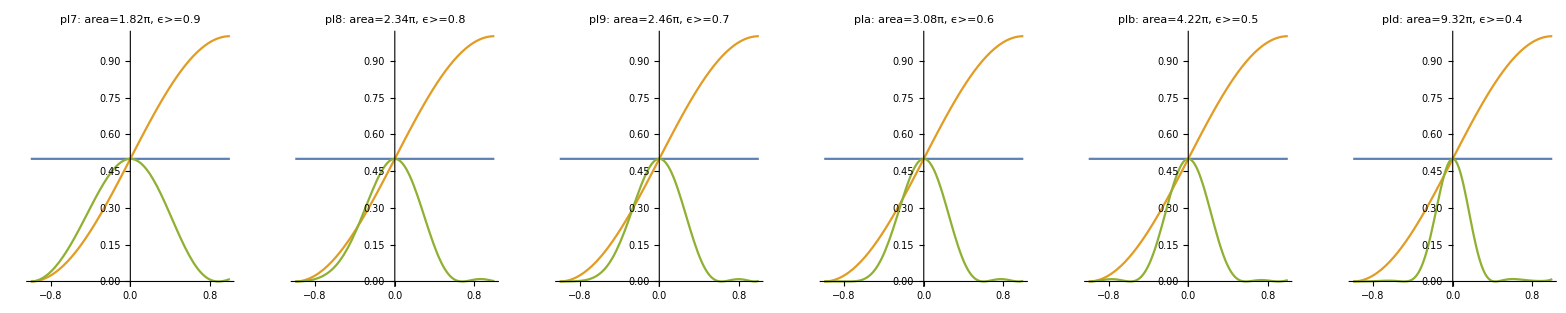

NB5; p=1/4

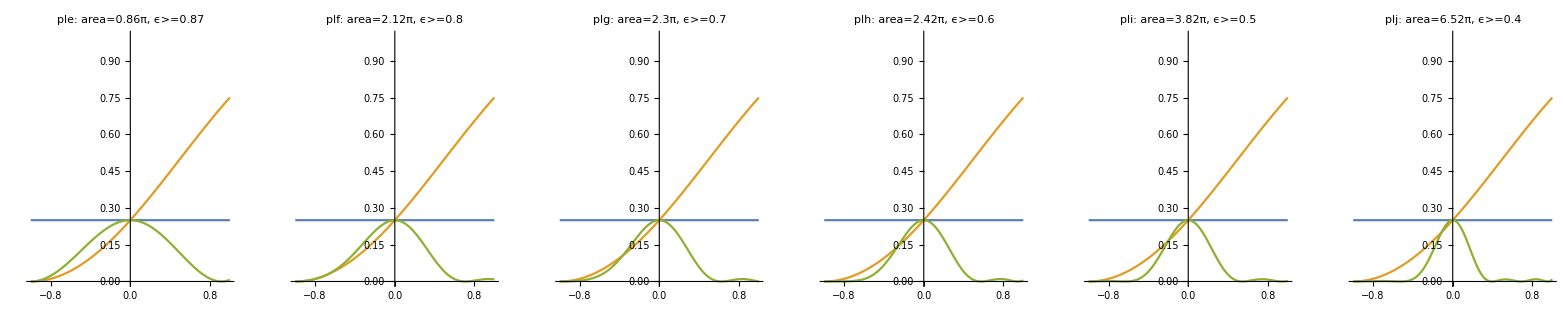

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,5]]

pl1=pltN[1.0,{Δ1->0.3322,Δ2->-0.7215,Δ3->-0.5428,Ω1->0.4499},"pl1"];
pl2=pltN[1.0,{Δ1->0.2742,Δ2->-0.6938,Δ3->-0.3613,Ω1->0.4907},"pl2"];
pl3=pltN[1.0,{Δ1->0.2564,Δ2->-0.6724,Δ3->-0.2989,Ω1->0.5093},"pl3"];
pl4=pltN[1.0,{Δ1->-0.0551,Δ2->0.8069,Δ3->-2.29298,Ω1->0.6571},"pl4"];
pl5=pltN[1.0,{Δ1->14.4705,Δ2->-1.7806,Δ3->6.1660,Ω1->1.8493},"pl6"];

pl7=pltN[0.5,{Δ1->0.6494,Δ2->0.355,Δ3->0.9830,Ω1->0.3648},"pl7"];
pl8=pltN[0.5,{Δ1->-0.0004,Δ2->0.8774,Δ3->0.0102,Ω1->0.4671},"pl8"];
pl9=pltN[0.5,{Δ1->0.2872,Δ2->-0.0903,Δ3->1.1205,Ω1->0.4919},"pl9"];
pla=pltN[0.5,{Δ1->0.1931,Δ2->0.0931,Δ3->4.7588,Ω1->0.6151},"pla"];
plb=pltN[0.5,{Δ1->0.3872,Δ2->6.4715,Δ3->-0.1170,Ω1->0.8443},"plb"];
plc=pltN[0.5,{Δ1->6.2267,Δ2->-1.6082,Δ3->6.5227,Ω1->1.8648},"pld"];

ple=pltN[0.25,{Δ1->0.0758,Δ2->0.2261,Δ3->0.2890,Ω1->0.1719},"ple"];
plf=pltN[0.25,{Δ1->0.2788,Δ2->-0.1892,Δ3->1.3333,Ω1->0.4237},"plf"];
plg=pltN[0.25,{Δ1->0.2599,Δ2->-0.1703,Δ3->1.2575,Ω1->0.4599},"plg"];
plh=pltN[0.25,{Δ1->0.2478,Δ2->-0.1637,Δ3->1.2071,Ω1->0.4836},"plh"];
pli=pltN[0.25,{Δ1->0.5228,Δ2->4.4980,Δ3->-0.1798,Ω1->0.7635},"pli"];
plj=pltN[0.25,{Δ1->0.7545,Δ2->-3.0646,Δ3->8.2698,Ω1->1.3039},"plj"];

GGrid[Text[Style["NB5; p=1",FontSize->20]],{{pl1,pl2,pl3,pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2",FontSize->20]],{{pl7,pl8,pl9,pla,plb,plc}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/4",FontSize->20]],{{ple,plf,plg,plh,pli,plj}},ImageSize->Full]
```

NB6; p=1

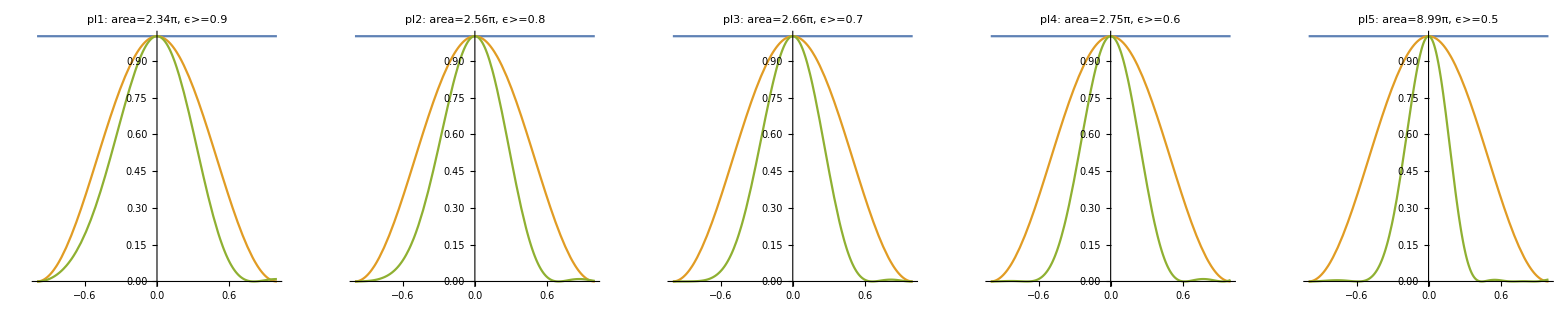

NB6; p=1/2

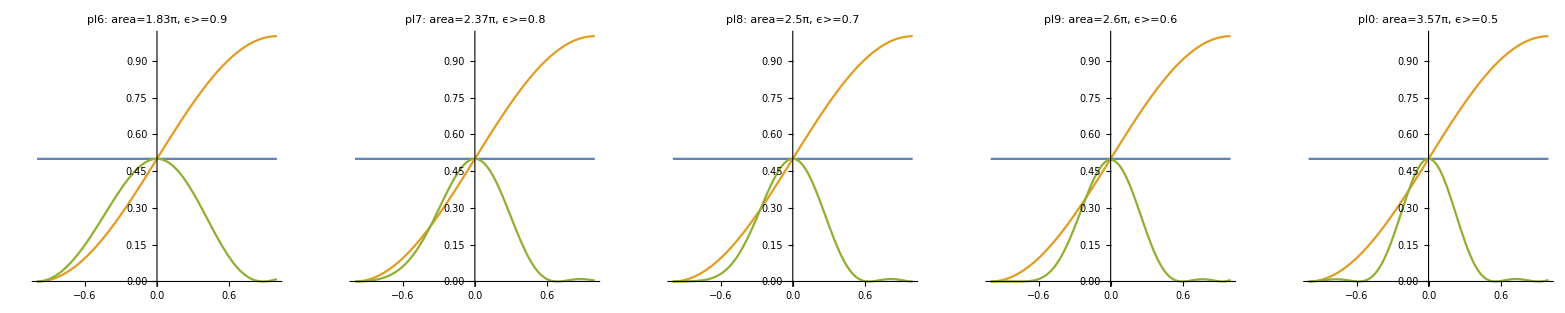

NB6; p=1/4

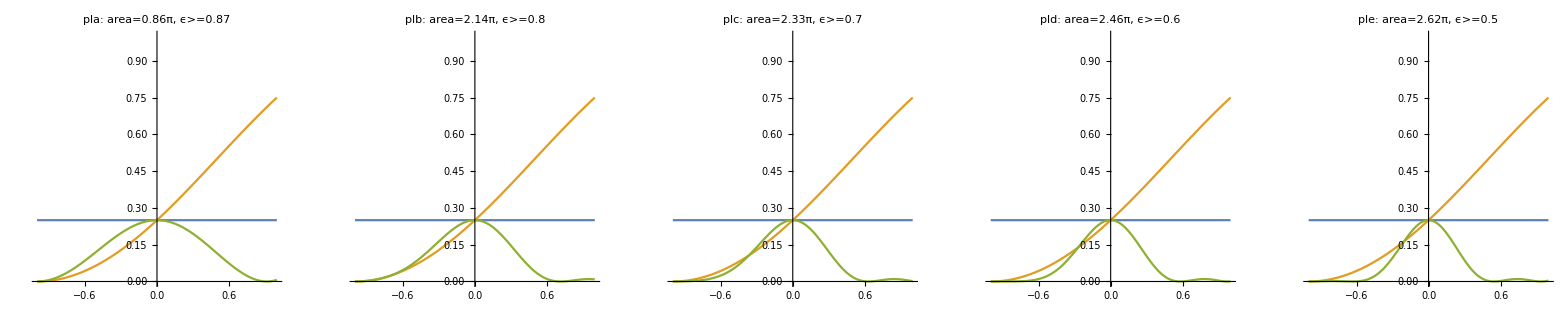

```mathematica
(*N=6 - SYM is BETTER*)
NPulses=6;
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label, totalArea[rule,6]]

pl1=pltS[1.0,{Δ1->-0.5056,Δ2->0.5407,Δ3->0.5161,Ω1->0.3896},"pl1"];
pl2=pltS[1.0,{Δ1->-0.4670,Δ2->0.5499,Δ3->0.4041,Ω1->0.4274},"pl2"];
pl3=pltS[1.0,{Δ1->0.4568,Δ2->-0.5469,Δ3->-0.3573,Ω1->0.4440},"pl3"];
pl4=pltS[1.0,{Δ1->0.4365,Δ2->-0.5339,Δ3->-0.3107,Ω1->0.4586},"pl4"];
pl5=pltS[1.0,{Δ1->2.0193,Δ2->-1.8045,Δ3->12.9873,Ω1->1.4978},"pl5"];

pl6=pltS[0.5,{Δ1->-0.5113,Δ2->0.0738,Δ3->0.8154,Ω1->0.3057},"pl6"];
pl7=pltS[0.5,{Δ1->-0.5705,Δ2->0.2520,Δ3->0.6080,Ω1->0.3958},"pl7"];
pl8=pltS[0.5,{Δ1->0.6874,Δ2->0.1438,Δ3->0.4403,Ω1->0.4167},"pl8"];
pl9=pltS[0.5,{Δ1->-0.6804,Δ2->-0.1261,Δ3->-0.4022,Ω1->0.4337},"pl9"];
pl0=pltS[0.5,{Δ1->-0.1547,Δ2->2.541,Δ3->0.2322,Ω1->0.5954},"pl0"];

pla=pltS[0.25,{Δ1->0.0546,Δ2->0.1584,Δ3->0.2308,Ω1->0.1432},"pla"];
plb=pltS[0.25,{Δ1->0.6038,Δ2->-0.1005,Δ3->-0.7157,Ω1->0.3570},"plb"];
plc=pltS[0.25,{Δ1->0.6066,Δ2->-0.1484,Δ3->-0.6511,Ω1->0.3885},"plc"];
pld=pltS[0.25,{Δ1->0.6060,Δ2->-0.1736,Δ3->-0.6074,Ω1->0.4096},"pld"];
ple=pltS[0.25,{Δ1->0.2584,Δ2->-0.8484,Δ3->-0.0721,Ω1->0.4370},"ple"];

GGrid[Text[Style["NB6; p=1",FontSize->20]],{{pl1,pl2,pl3,pl4,pl5}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/2",FontSize->20]],{{pl6,pl7,pl8,pl9,pl0}},ImageSize->Full]
GGrid[Text[Style["NB6; p=1/4",FontSize->20]],{{pla,plb,plc,pld,ple}},ImageSize->Full]
```

NB7; p=1

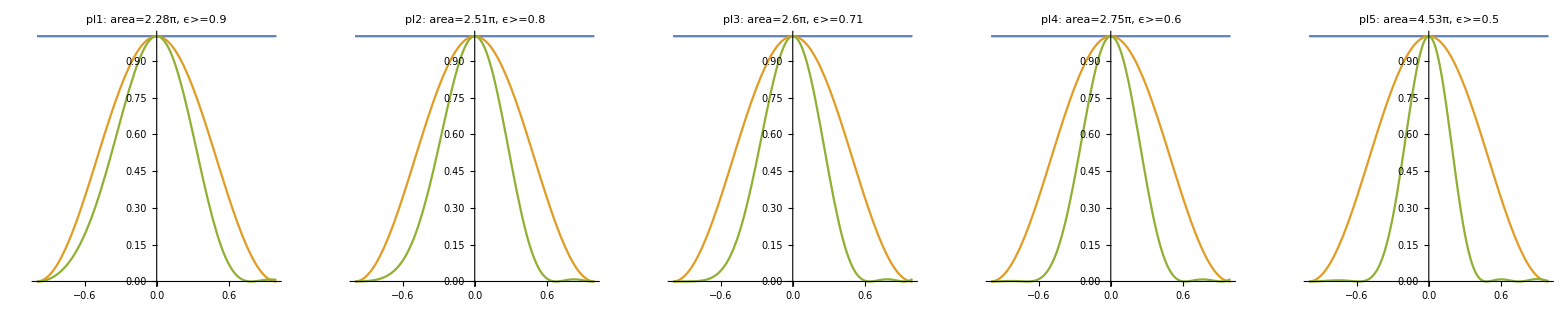

NB7; p=1/2

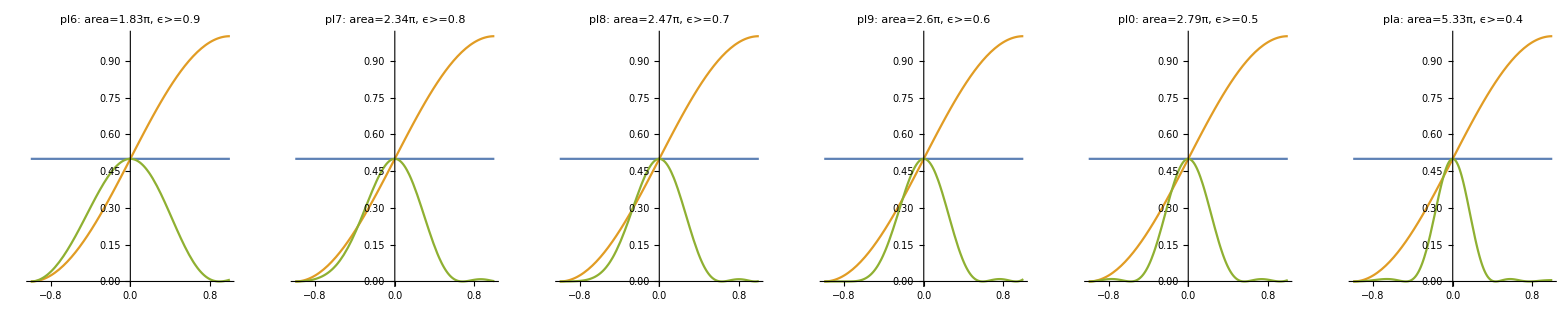

NB7; p=1/4

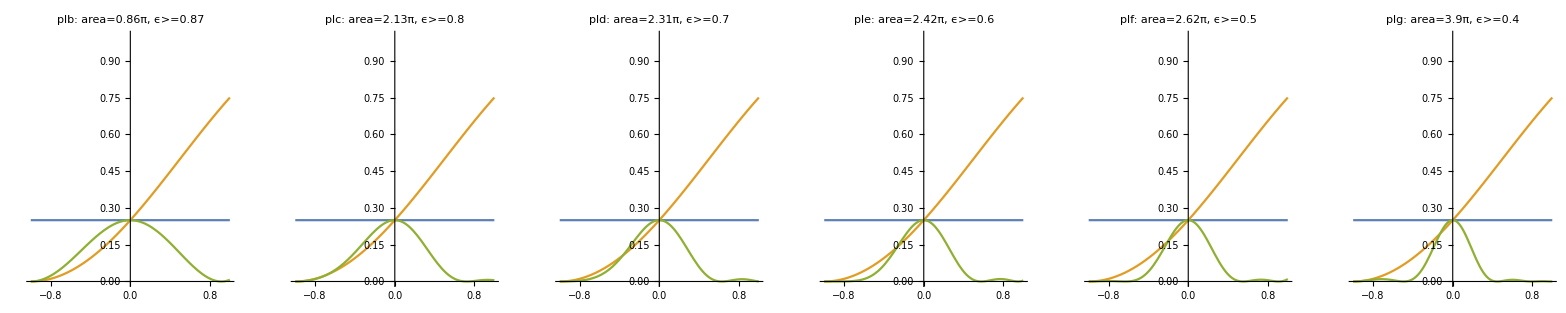

```mathematica
(*N=7 - slightly better than NB6 - Choose this*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,7]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,0,label, totalArea[rule,7]]

pl1=pltS[1.0,{Δ1->0.3500,Δ2->0.1892,Δ3->0.1049,Δ4->0.8853,Ω1->0.3251},"pl1"];
pl2=pltS[1.0,{Δ1->0.3655,Δ2->0.1575,Δ3->0.0869,Δ4->0.7761,Ω1->0.3579},"pl2"];
pl3=pltS[1.0,{Δ1->0.3105,Δ2->0.1990,Δ3->0.0207,Δ4->0.7817,Ω1->0.3717},"pl3"];
pl4=pltS[1.0,{Δ1->0.1989,Δ2->0.2980,Δ3->-0.1225,Δ4->0.8546,Ω1->0.3935},"pl4"];
pl5=pltS[1.0,{Δ1->0.2221,Δ2->0.9420,Δ3->-0.0018,Δ4->2.4957,Ω1->0.6471},"pl5"];

pl6=pltS[0.5,{Δ1->-0.3513,Δ2->-0.1726,Δ3->0.5998,Δ4->0.7109,Ω1->0.2617},"pl6"];
pl7=pltS[0.5,{Δ1->0.4101,Δ2->0.0226,Δ3->-0.5629,Δ4->-0.4330,Ω1->0.3347},"pl7"];
pl8=pltS[0.5,{Δ1->-0.4465,Δ2->0.0284,Δ3->0.5153,Δ4->0.4033,Ω1->0.3533},"pl8"];
pl9=pltS[0.5,{Δ1->0.6202,Δ2->0.1766,Δ3->0.2040,Δ4->0.4392,Ω1->0.3712},"pl9"];
pl0=pltS[0.5,{Δ1->0.7102,Δ2->0.0700,Δ3->0.2621,Δ4->0.3093,Ω1->0.3987},"pl0"];
pla=pltS[0.5,{Δ1->2.6276,Δ2->0.5897,Δ3->0.6125,Δ4->0.3015,Ω1->0.7608},"pla"];

plb=pltS[0.25,{Δ1->0.0402,Δ2->0.1176,Δ3->0.1807,Δ4->0.2059,Ω1->0.1228},"plb"];
plc=pltS[0.25,{Δ1->0.5808,Δ2->0.3985,Δ3->0.1535,Δ4->0.64,Ω1->0.3047},"plc"];
pld=pltS[0.25,{Δ1->0.3819,Δ2->0.1645,Δ3->-0.6076,Δ4->-0.4464,Ω1->0.3296},"pld"];
ple=pltS[0.25,{Δ1->-0.4166,Δ2->-0.1114,Δ3->0.5636,Δ4->0.4220,Ω1->0.3463},"ple"];
plf=pltS[0.25,{Δ1->0.0215,Δ2->0.1405,Δ3->-0.1601,Δ4->1.1209,Ω1->0.3741},"plf"];
plg=pltS[0.25,{Δ1->-0.5557,Δ2->0.9030,Δ3->0.6447,Δ4->0.0490,Ω1->0.5577},"plg"];

GGrid[Text[Style["NB7; p=1",FontSize->20]],{{pl1,pl2,pl3,pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/2",FontSize->20]],{{pl6,pl7,pl8,pl9,pl0,pla}},ImageSize->Full]
GGrid[Text[Style["NB7; p=1/4",FontSize->20]],{{plb,plc,pld,ple,plf,plg}},ImageSize->Full]
```